```mathematica
Select[Range[100],VertexCount[ReadGrof[#]]==6&]
```

{3,4}

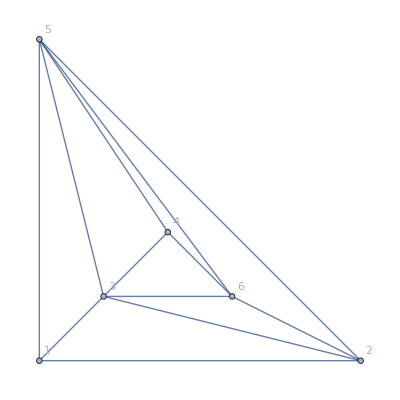
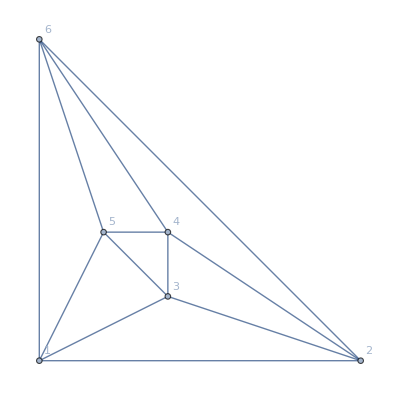

```mathematica
Table[Graph[ReadGrof[k],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"],{k,{3,4}}]
```

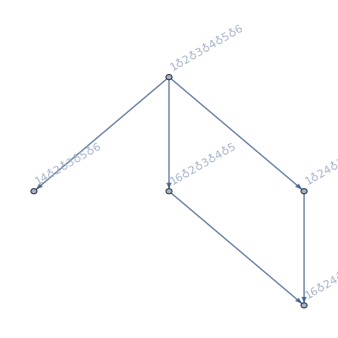
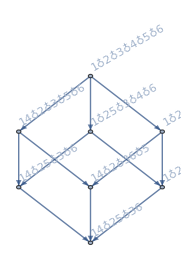

```mathematica
Table[FormulaGraphReverse2[FindFullFormula[Graph[ReadGrof[k],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]]],{k,{3,4}}]
```

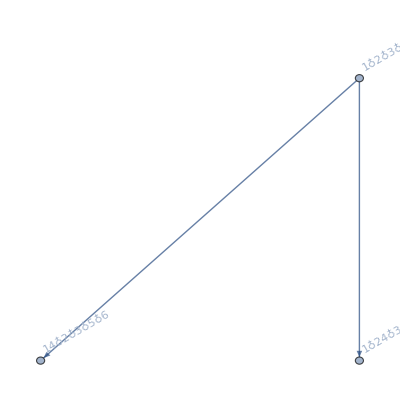
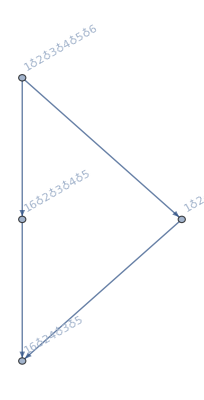
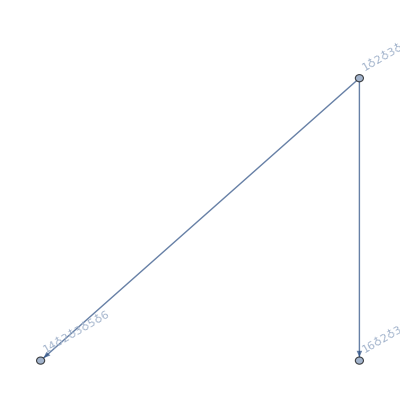
{1<->6→-Graphics-,1<->4→-Graphics-,2<->4→-Graphics-}

```mathematica
With[{g=ReadGrof[3]},
Table[e->FormulaGraphReverse2[FindFullFormula[EdgeAdd[g,e]]] ,{e,EdgeList[GraphComplement[g]]}]
]
```

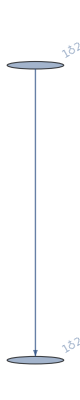
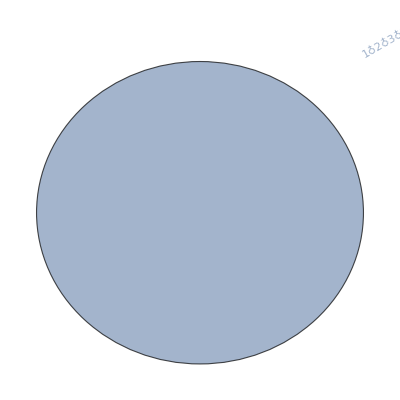
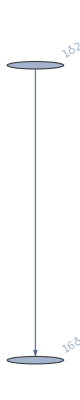
{1<->6→-Graphics-,1<->4→-Graphics-,2<->4→-Graphics-}

```mathematica
With[{g=ReadGrof[3]},
Table[e->FormulaGraphReverse2[FindFullFormula[VertexContract[g,{e[[1]],e[[2]]}]]] ,{e,EdgeList[GraphComplement[g]]}]
]
```

```mathematica
Select[Range[100],VertexCount[ReadGrof[#]]==7&]
```

{5,6,7,8,9}

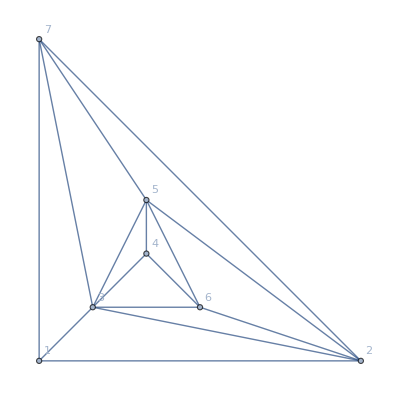
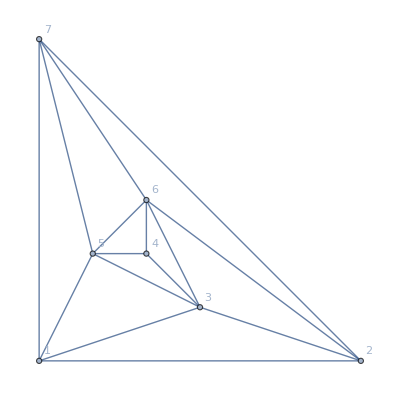
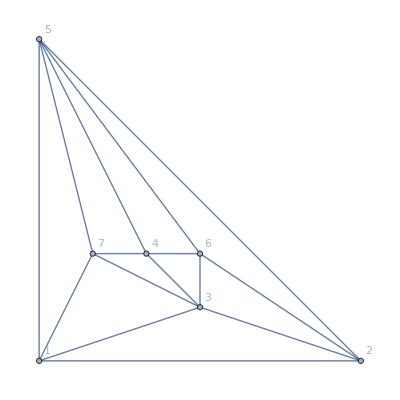
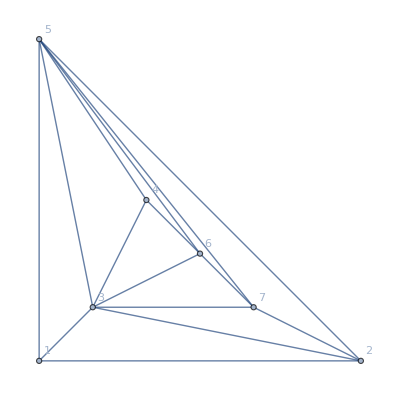
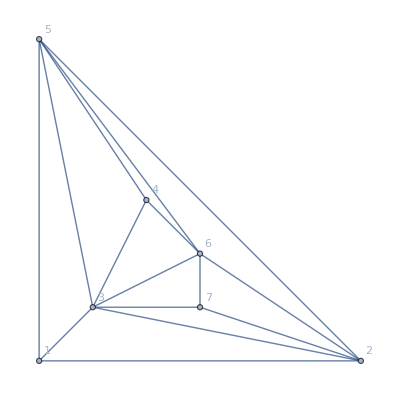

```mathematica
Table[Graph[ReadGrof[k],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"],{k,{5,6,7,8,9}}]
```

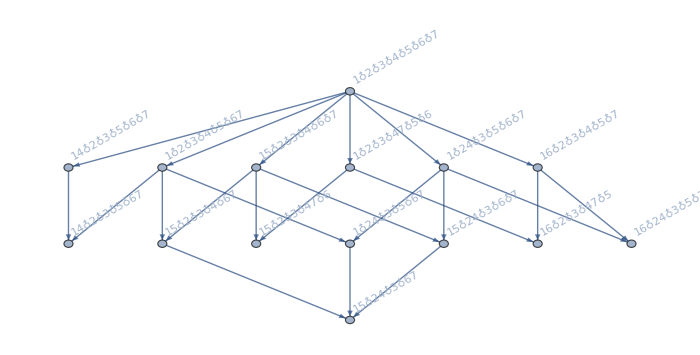
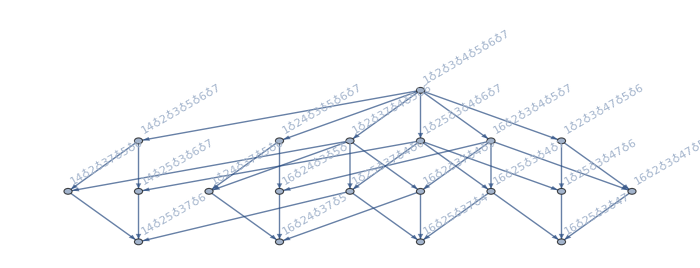
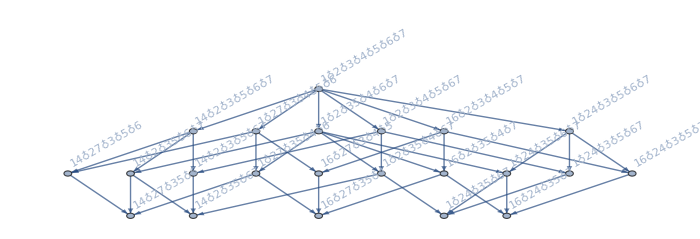
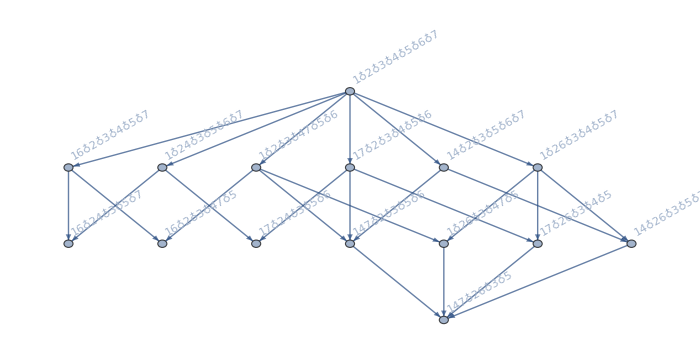
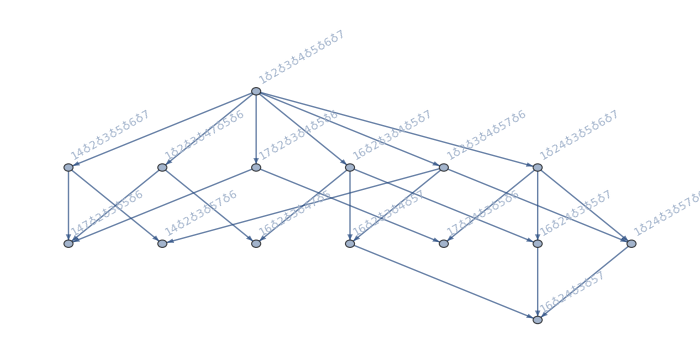

```mathematica
Table[Graph[FormulaGraphReverse2[FindFullFormula[Graph[ReadGrof[k],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]]],ImageSize->700],{k,{5,6,7,8,9}}]
```